# Three-point function of the model on the cylinder of size 4

```mathematica
Needs["Developer`"]; On[Assert]
```

The module  for the  model in size  has two states labelled .
The module  for the  model in size  has 4 states. To compute three-point functions, we need to introduce labels  on the defects indicating where they are coming from. We label the states in as , where i and j are the positions of the two defects, and a indicates the labels: R_1 R_1 <=> a=0  R_1 R_2 <=> a=1  R_2 R_1 <=> a=2 R_2 R_2 <=> a=4
 Thus, the computation of all the

for the three point function   involves link patterns with 0, 2 or 4 defects, and with labels  indicating where the labels come from. We call  the state with defects at positions 1 and 2, and labels 

We construct the transfer matrix

and the operator  defined in the draft paper PottsOn/articles/three-point/vvv_loops.tex.

## Module

To compute the action of the generators  we compute  and define , where  is the translation operator.

```mathematica
e1 = {{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, -1}, {0, 0, 0, n}}//Transpose;
u = {{0, 0, 1, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 1, 0, 0}}//Transpose;
(* u = {{0, 0, 1, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, -1, 0, 0}}//Transpose; *) 
ui[i_] := MatrixPower[u, i]
e[i_] := ui[i-1].e1.ui[1-i]
e1 = e[1]; e2 = e[2]; e3 = e[3]; e4 = e[4];
id = IdentityMatrix[4];
T = (id+ e[1]).(id+e[2]).(id+ e[3]).(id+e[4]);
P = {{0, 0, 0, 1}, {0, 1, 0, 0}, {0, 0, 1, 0}, {1, 0, 0, 0}}//Transpose;
```

```mathematica
(* check that all algebraic relations are verified *)
algRel = Join[
Table[e[i].e[i] - n*e[i], {i, 1, 4}], (*  *)
Table[ui[1].e[i].ui[-1] - e[i+1], {i,1,4}], (*  *)
Table[e[i+4]-e[i], {i,5, 8}], (*  *)
Table[e[i+1].e[i].e[i+1] - e[i+1], {i, 1, 4}], (*  *)
Table[e[i].e[i+1].e[i] - e[i], {i, 1, 4}] (*  *)
];
AppendTo[algRel,ui[2].e[3] - e[1].e[2].e[3]]; (*  *)

UPTRel = {};
AppendTo[UPTRel, P.u - ui[-1].P]; 
AppendTo[UPTRel, T.ui[2] - ui[2].T]; 
AppendTo[UPTRel, T.P - P.T]; 

Assert[algRel==Table[Table[0, {4}, {4}], Length[algRel]]];
Assert[UPTRel==Table[Table[0, {4}, {4}], Length[UPTRel]]];
```

```mathematica
(* left and right eigenvectors *)
ev = Eigenvalues[T];
evr = Eigenvectors[T]; evr /= Table[Norm[evr[[i]]], {i, 1, 4}] // Simplify;
evl = Eigenvectors[T//Transpose]; evl /= Table[Norm[evl[[i]]], {i, 1, 4}] // Simplify;
Assert[Table[T.evr[[i]] - ev[[i]]*evr[[i]]//Simplify, {i, 1, 4}]==Table[{0, 0, 0, 0}, {4}]]
Assert[Table[Transpose[T].evl[[i]] - ev[[i]]*evl[[i]]//Simplify, {i, 1, 4}]==Table[{0, 0, 0, 0}, {4}]]
```

```mathematica
(* Check that  *)
Sum[1/(evl[[i]]ᵀ.evr[[i]]) *Outer[Times, evr[[i]], evl[[i]]], {i,1,4} ]/.{n->Sqrt[1.4]}//N//(Round[#, 0.00001] &) // MatrixForm
```

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.)

```mathematica
(* T = (2+n) * 11 - n*id  *)
T4 = (2+n)*Table[1, {i, 1, 4}, {j, 1, 4}]  - n*IdentityMatrix[4];
TT4[M_]:=MatrixPower[T4, M]
T2 = {{4+3*n, 4+4*n+n^2},{ 4+4*n+n^2, 4+3*n}};
TT2[M_] := MatrixPower[T2, M]
G4 = n IdentityMatrix[4] + {{0, 1, 1, 0}, {1, 0, 0, 1}, {1, 0, 0, 1}, {0, 1, 1, 0}};
G2 = {{n^2, n}, {n, n^2}};
O22 = {{n, 1, 1, 0},{1, n, 0, 1},{1, 0, 0, 1},{0, 1, 1,0}};
O02 = {{n, 1, 0, 1},{1, 0, 1, n}};
Z000[M_]:= {1, 0}.G2.TT2[2*M].{1, 0}//Expand
Z222[M_] :=(TT4[M].{1, 0, 0, 0})ᵀ.O22.(TT4[M].{1, 0, 0, 0})//Expand
Z202[M_]:={1, 0, 0, 0}ᵀ.G4.TT4[2*M].{1, 0, 0, 0}//Expand
Z220[M_] := (TT2[M].{1, 0})ᵀ.O02.TT4[M].{1, 0, 0, 0}//Expand
```

```mathematica
λs = Table[Pi * βsq/4, {βsq, 0.5+0.01, 1.5-0.01, 0.01}];
nλ[λ_] := -2*Cos[4*λ];
ns = nλ/@λs;
ω[M_]:=Z222[M]/Z220[M]*Sqrt[Z202[M]*Z000[M]/Z202[M]/Z202[M]]
```

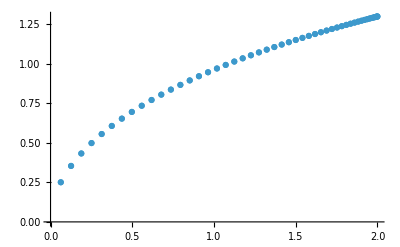

```mathematica
ListPlot[Table[{ns[[i]],ω[10]/.{n->ns[[i]]}}, {i, 1, Length[ns]}]]
```

```mathematica
Z222[1]
```

32+32 n+8 n^2+n^3

```mathematica
gramSchmidtG[vectors_,G_]:=Module[{u={},vi,wi},Do[vi=vectors[[i]];
wi=Fold[#1-(Transpose[#2].G.vi)/(Transpose[#2].G.#2)*#2&,vi,u];
wi=wi/Sqrt[Transpose[wi].G.wi];(*Normalize wrt G*)AppendTo[u,wi],{i,Length[vectors]}];
u]
{vals4, vecs4} = Eigensystem[T4];
vecs4=gramSchmidtG[vecs4,G4] // Simplify;
{vals2,vecs2}=Eigensystem[T2];
vecs2=gramSchmidtG[vecs2,G2] // Simplify;
```

```mathematica
pos4 = First@Ordering[vals4/.n->10,-1];
First@Ordering[vals2/.n->10,-1];
v2 = vecs4[[pos4]]
v0 = vecs2[[pos2]]
formfactorRatio =(v2ᵀ.O22.v2)/(v2ᵀ.O02ᵀ.v0)(v2.G4.{1, 0, 0, 0})/(v0.G2.{1, 0})Sqrt[((v0ᵀ.G2.{1, 0})*({1, 0}.G2.v0))/((v2.G4.{1, 0, 0, 0})*({1, 0, 0, 0}.G4.v2))]//FullSimplify
(v2.G4.{1, 0, 0, 0})/(v0.G2.{1, 0})Sqrt[((v0ᵀ.G2.{1, 0})*({1, 0}.G2.v0))/((v2.G4.{1, 0, 0, 0})*({1, 0, 0, 0}.G4.v2))]//FullSimplify
```

{1/(2 √(2+n)),1/(2 √(2+n)),1/(2 √(2+n)),1/(2 √(2+n))}

{1/(√(2 n+2 n^2)),1/(√(2 n+2 n^2))}

((4+n) √((n+n^2)/(4+2 n)))/(2+n)

(√((n (1+n))/(2+n)) √(2+n))/(√(n (1+n)))

```mathematica
(v2.G4.{1, 0, 0, 0})/(v0.G2.{1, 0})Sqrt[((v0ᵀ.G2.{1, 0})*({1, 0}.G2.v0))/((v2.G4.{1, 0, 0, 0})*({1, 0, 0, 0}.G4.v2))]
```

((1/(√(2+n))+n/(2 √(2+n))) √(((n/(√(2 n+2 n^2))+n^2/(√(2 n+2 n^2)))^2)/(1/(√(2+n))+n/(2 √(2+n)))^2))/(n/(√(2 n+2 n^2))+n^2/(√(2 n+2 n^2)))

```mathematica
{vals4,vecs4}=Eigensystem[T4];
vecs4 = Orthogonalize[vecs4];
vecs4 = Normalize/@vecs4;
pos4=First@Ordering[vals4/.n->10,-1];
v2 = vecs4[[pos4]];
{vals2,vecs2}=Eigensystem[T2];
vecs2 = Normalize/@vecs2;
pos2=First@Ordering[vals2/.n->10,-1];
v0 = vecs2[[pos2]];
formfactorRatio =(v2ᵀ.O22.v2)/(v2ᵀ.O02ᵀ.v0)(v2.{1, 0, 0, 0})/(v0.{1, 0})Sqrt[((v0ᵀ.G2.{1, 0})*({1, 0}.v0))/((v2.G4.{1, 0, 0, 0})*({1, 0, 0, 0}.v2))]//FullSimplify
```

((4+n) √((n+n^2)/(4+2 n)))/(2+n)

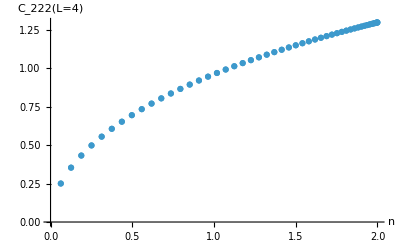

```mathematica
ListPlot[
Table[{ns[[i]], formfactorRatio/.n->ns[[i]]}, {i, 0, Length[ns]}],
Axes->True,
AxesLabel->{n, "C_222(L=4)"}]
```

```mathematica
Block[{n=1.2, M=10},{
Z222[M],
(v2.{1, 0, 0, 0})^2*vals4[[pos4]]^(2*M)*v2ᵀ.O22.v2,
Z220[M],
(v2.{1, 0, 0, 0})(v0.{1, 0})*vals4[[pos4]]^M*vals2[[pos2]]^M*v0ᵀ.O02.v2,
Z202[M],
(v2.{1, 0, 0, 0})(v2.G4.{1, 0, 0, 0})*vals4[[pos4]]^(2M),
Z000[M],
(v0ᵀ.G2.{1, 0})(v0.{1, 0})*vals2[[pos2]]^(2M),
ω[M],
Z222[M] / Z220[M] *Sqrt[ Z000[M]/Z202[M]],
formfactorRatio/Sqrt[2],
(v2.{1, 0, 0, 0})^2*vals4[[pos4]]^(2*M)*v2ᵀ.O22.v2 / ((v2.{1, 0, 0, 0})(v0.{1, 0})*vals4[[pos4]]^M*vals2[[pos2]]^M*v0ᵀ.O02.v2)*Sqrt[(v0ᵀ.G2.{1, 0})(v0.{1, 0})*vals2[[pos2]]^(2M)/((v2.{1, 0, 0, 0})(v2.G4.{1, 0, 0, 0})*vals4[[pos4]]^(2M))],
(v2.{1, 0, 0, 0})*v2ᵀ.O22.v2 / ((v0.{1, 0})*v0ᵀ.O02.v2)*Sqrt[(v0ᵀ.G2.{1, 0})(v0.{1, 0})/((v2.{1, 0, 0, 0})(v2.G4.{1, 0, 0, 0}))],
(v2ᵀ.O22.v2)/(v2ᵀ.O02ᵀ.v0)(v2.{1, 0, 0, 0})/(v0.{1, 0})Sqrt[((v0ᵀ.G2.{1, 0})*({1, 0}.v0))/((v2.G4.{1, 0, 0, 0})*({1, 0, 0, 0}.v2))]
}
]
```

{1.26495×10^21,1.26495×10^21,1.15244×10^23,1.15244×10^23,1.55686×10^21,1.55686×10^21,1.40757×10^25,1.40757×10^25,1.04368,1.04368,1.04368,1.04368,1.04368,1.04368}

```mathematica
vals4[[pos4]]^M/.n->1.2
```

4.41144×10^10

```mathematica
Sum[KroneckerProduct[vecs4[[i]],vecs4[[i]]ᵀ], {i, 1, 4}];
%//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

### Check with the 12x12 transfer matrix acting on states with labelled defects:

```mathematica
u12 =Normal[PermutationMatrix[{2, 3, 4, 1, 6, 7, 8, 5, 10, 11, 12, 9}]]ᵀ;
T12row1 = {0, n+2, 0, n+2, 2, 0, n+2, 0, 0, 0, 0, 0};
T12row5 = {2, 0, n+2, 0, 0, n+2, 0, n+2, 0, 0, 0, 0}; (* (n+2)(6 + 8 + 3) + 2*1 *)
T12row9 = {0, 1, 1, 1, 1, 1, 0, 1, 0, 1, 0, 1};
T12 = Join[Table[MatrixPower[u12, N].T12row1, {N, 0, 3}],
Table[MatrixPower[u12, N].T12row5, {N, 0, 3}],
Table[MatrixPower[u12, N].T12row9, {N, 0, 3}]]ᵀ;
TT12[M_] := MatrixPower[T12, M]
O412 = {{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0},
{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0},
{0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}}ᵀ;
P12 = {n, 1, 0, 1, n , 1, 0, 1, 1, 0, 1, 0}ᵀ;
Z222form2[M_] := P12.TT12[M].O412.TT4[M].{1, 0, 0, 0}//Expand
Z222form2[1]
Z222form2[2]
```